```mathematica
d2fdϕ2 = FullSimplify[((ya-yb)(1/(y(y+1))-Log[1+y]/y^2)(ya/va-yb/vb) + 1/2(ya-yb)^2 ((2Log[1+y])/y^3-(2+3 y)/((y+y^2)^2))(ϕ ya/va+(1-ϕ)yb/vb)+1/(va ϕ)+1/(vb(1-ϕ)))/.{y-> ϕ ya + (1-ϕ) yb}/.{vb-> v, va-> v}]
(* The last line with arrows are substitution steps *)
(* I have set ϕ=ϕa, 1-ϕ=ϕb *)
```

```mathematica
-(2/(-1+ϕ)-2/ϕ+(ya-yb)^2/(1+yb+ya ϕ-yb ϕ)^2)/(2 v)
derivative[ya_, yb_, v_, ϕ_] := -(2/(-1+ϕ)-2/ϕ+(ya-yb)^2/(1+yb+ya ϕ-yb ϕ)^2)/(2 v)
```

-(2/(-1+ϕ)-2/ϕ+(ya-yb)^2/(1+yb+ya ϕ-yb ϕ)^2)/(2 v)

```mathematica
(* This last line now looks simple enough -- can we tell when d2f/dϕ2 = 0 has a solution? *)

Solve[-(2/(-1+ϕ)-2/ϕ+(ya-yb)^2/(1+yb+ya ϕ-yb ϕ)^2)/(2 v)==0 , ya]
```

```mathematica
{{ya->(-2 ϕ-3 yb ϕ+3 yb ϕ^2-√2 √(ϕ+2 yb ϕ+yb^2 ϕ-ϕ^2-2 yb ϕ^2-yb^2 ϕ^2))/(-ϕ+3 ϕ^2)},{ya->(-2 ϕ-3 yb ϕ+3 yb ϕ^2+√2 √(ϕ+2 yb ϕ+yb^2 ϕ-ϕ^2-2 yb ϕ^2-yb^2 ϕ^2))/(-ϕ+3 ϕ^2)}}

(* Plotting the two solutions below *)
```

```mathematica
f[ϕ_, yb_]:=(-2 ϕ-3 yb ϕ+3 yb ϕ^2-√2 √(ϕ+2 yb ϕ+yb^2 ϕ-ϕ^2-2 yb ϕ^2-yb^2 ϕ^2))/(-ϕ+3 ϕ^2)
```

```mathematica
f[0.3, 2]
```

```mathematica
126.80740698407871

Plot3D[f[ϕ,yb],{ϕ, 0.01, 0.99}, {yb, 0, 40}, PlotRange->Automatic]
```

126.807

-Graphics3D-

```mathematica
Plot3D[f[ϕ,yb],{ϕ, 0.01, 0.99}, {yb, 0, 40}, PlotRange->{{0.01, 0.99},{0, 40},{0, 800}}]
```

-Graphics3D-

```mathematica
derivative[600, 10, 70, 0.1]
```

```mathematica
-0.3487042436022028
(* So if a line never crossed/goes above the arc region, the substances for those ya and yb are miscible at any ratios *)
```

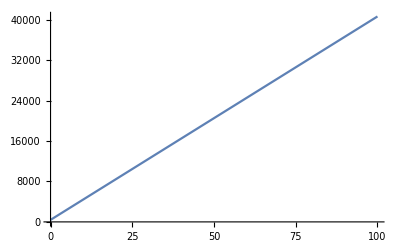

```mathematica
Plot[f[0.33,yb], {yb, 0, 100}, PlotRange->Automatic]
```

```mathematica
(* The function is increasing for ϕ=(0, 0.33] and decreasing for ϕ=[0.34, 1) *)
```

```mathematica
h[ϕ_, yb_]:=(-2 ϕ-3 yb ϕ+3 yb ϕ^2+√2 √(ϕ+2 yb ϕ+yb^2 ϕ-ϕ^2-2 yb ϕ^2-yb^2 ϕ^2))/(-ϕ+3 ϕ^2)
```

```mathematica
Plot3D[h[ϕ,yb],{ϕ, 0.01, 0.99}, {yb, 0, 40}, PlotRange->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[h[ϕ,yb],{ϕ, 0.01, 0.99}, {yb, 0, 40}, PlotRange->{{0.01, 0.99},{0, 40},{0, 4}}]
```

-Graphics3D-

```mathematica
derivative[1, 30, 70, 0.9]
```

```mathematica
-0.09146321307920656
(* So if a line never crosses/goes below the arc region, the substances for those ya and yb are miscible at any ratios *)
```

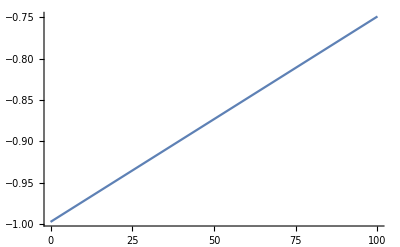

```mathematica
Plot[h[0.67,yb], {yb, 0, 100}, PlotRange->Automatic]
(* The function is decreasing for ϕ=(0, 0.66] and increasing for ϕ=[0.67, 1) *)
```

```mathematica
Plot3D[{f[ϕ,yb],h[ϕ,yb]},{ϕ, 0.01, 0.99}, {yb, 0, 40}, PlotRange->{{0.01, 0.99},{0, 40},{0, 800}}]
```

-Graphics3D-

```mathematica
(* When yb and vb are fixed (water): *)
```

```mathematica
d2fdϕ2 = FullSimplify[((ya-yb)(1/(y(y+1))-Log[1+y]/y^2)(ya/va-yb/vb) + 1/2(ya-yb)^2 ((2Log[1+y])/y^3-(2+3 y)/((y+y^2)^2))(ϕ ya/va+(1-ϕ)yb/vb)+1/(va ϕ)+1/(vb(1-ϕ)))/.{y-> ϕ ya + (1-ϕ) yb}/.{vb-> 30, yb-> 29.8}]
```

1/(30-30 ϕ)+1/(va ϕ)+1/2 (-29.8+ya)^2 (0.993333+(-0.993333+ya/va) ϕ) ((-91.4+(89.4-3. ya) ϕ)/(917.84+ϕ (-1805.88+888.04 ϕ+ya (60.6+(-59.6+ya) ϕ)))^2+(2. Log[30.8+(-29.8+ya) ϕ])/(29.8+(-29.8+ya) ϕ)^3)-(1. (-29.8+ya) (-0.993333 va+ya) (-29.8+(29.8-1. ya) ϕ+(30.8+(-29.8+ya) ϕ) Log[30.8+(-29.8+ya) ϕ]))/(va (29.8+(-29.8+ya) ϕ)^2 (30.8+(-29.8+ya) ϕ))